```mathematica
Clear[x,A]
```

```mathematica
a=-5/128;
b=-1/128;
y=x/6;
c=x/(2Sqrt[6]);
d=x/(3Sqrt[2]);
```

```mathematica
A[x_]={{a-x/2,0,0,0,0,-c,0,0},{0,a+x/2,0,0,0,0,c,0},{0,0,a-y,0,0,-d,0,0},{0,0,0,a+y,0,0,-d,0},{0,0,0,0,b-x,0,0,0},{-c,0,-d,0,0,b-2y,0,0},{0,c,0,-d,0,0,b+2y,0},{0,0,0,0,0,0,0,b+x}};
```

```mathematica
A[x]//MatrixForm
```

(-5/128-x/2 | 0 | 0 | 0 | 0 | -x/(2 √6) | 0 | 0
0 | -5/128+x/2 | 0 | 0 | 0 | 0 | x/(2 √6) | 0
0 | 0 | -5/128-x/6 | 0 | 0 | -x/(3 √2) | 0 | 0
0 | 0 | 0 | -5/128+x/6 | 0 | 0 | -x/(3 √2) | 0
0 | 0 | 0 | 0 | -1/128-x | 0 | 0 | 0
-x/(2 √6) | 0 | -x/(3 √2) | 0 | 0 | -1/128-x/3 | 0 | 0
0 | x/(2 √6) | 0 | -x/(3 √2) | 0 | 0 | -1/128+x/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/128+x)

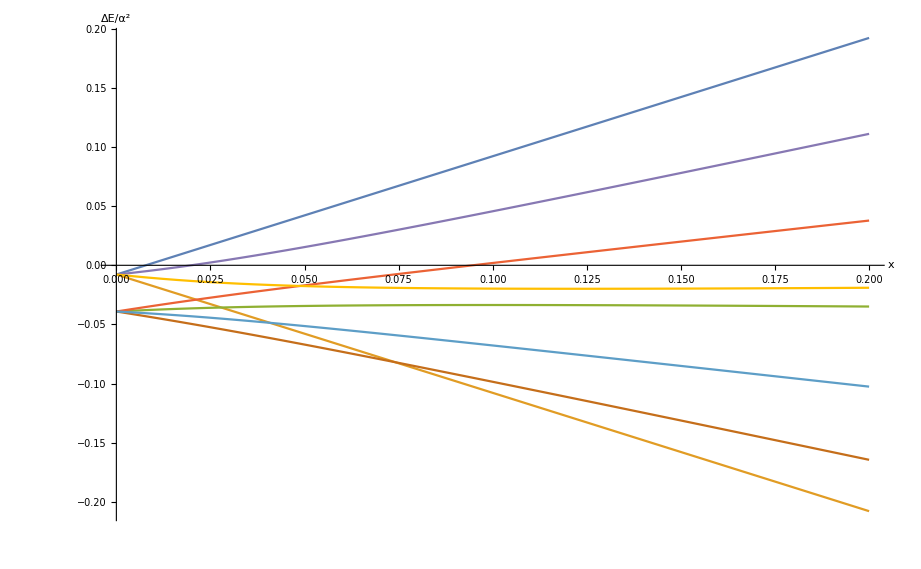

```mathematica
Plot[Evaluate[Eigenvalues[A[x]]],{x,0,0.2},AxesLabel->{x,ΔE/α^2}]
```

```mathematica
FullSimplify[Eigenvalues[A[x]],Assumptions->Element[x,Reals]]//ToRadicals
```

{-1/128+x,-1/128-x,1/384 (-11+128 x-(-144-55296 x^2)/(36 (1+192 x^2-1024 x^3+16 √(-3 x^2-8 x^3-1584 x^4-1536 x^5-217088 x^6))^(1/3))+4 (1+192 x^2-1024 x^3+16 √(-3 x^2-8 x^3-1584 x^4-1536 x^5-217088 x^6))^(1/3)),1/384 (-11+128 x+((1+ⅈ √3) (-144-55296 x^2))/(72 (1+192 x^2-1024 x^3+16 √(-3 x^2-8 x^3-1584 x^4-1536 x^5-217088 x^6))^(1/3))-2 (1-ⅈ √3) (1+192 x^2-1024 x^3+16 √(-3 x^2-8 x^3-1584 x^4-1536 x^5-217088 x^6))^(1/3)),1/384 (-11+128 x+((1-ⅈ √3) (-144-55296 x^2))/(72 (1+192 x^2-1024 x^3+16 √(-3 x^2-8 x^3-1584 x^4-1536 x^5-217088 x^6))^(1/3))-2 (1+ⅈ √3) (1+192 x^2-1024 x^3+16 √(-3 x^2-8 x^3-1584 x^4-1536 x^5-217088 x^6))^(1/3)),1/384 (-11-128 x-(-144-55296 x^2)/(36 (1+192 x^2+1024 x^3+16 √(-3 x^2+8 x^3-1584 x^4+1536 x^5-217088 x^6))^(1/3))+4 (1+192 x^2+1024 x^3+16 √(-3 x^2+8 x^3-1584 x^4+1536 x^5-217088 x^6))^(1/3)),1/384 (-11-128 x+((1+ⅈ √3) (-144-55296 x^2))/(72 (1+192 x^2+1024 x^3+16 √(-3 x^2+8 x^3-1584 x^4+1536 x^5-217088 x^6))^(1/3))-2 (1-ⅈ √3) (1+192 x^2+1024 x^3+16 √(-3 x^2+8 x^3-1584 x^4+1536 x^5-217088 x^6))^(1/3)),1/384 (-11-128 x+((1-ⅈ √3) (-144-55296 x^2))/(72 (1+192 x^2+1024 x^3+16 √(-3 x^2+8 x^3-1584 x^4+1536 x^5-217088 x^6))^(1/3))-2 (1+ⅈ √3) (1+192 x^2+1024 x^3+16 √(-3 x^2+8 x^3-1584 x^4+1536 x^5-217088 x^6))^(1/3))}

```mathematica
Series[FullSimplify[Eigenvalues[A[x]],Assumptions->Element[x,Reals]],{x,0,1}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of 675-40320 x+313344 x^2+393216 x^3+(315-8448 x+30720 x^2) #1+(33-384 x) #1^2+#1^3& for some values of x.

Root::sbr: Because of branch cuts, the series may represent a different root of 675+40320 x+313344 x^2-393216 x^3+(315+8448 x+30720 x^2) #1+(33+384 x) #1^2+#1^3& for some values of x.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

{-1/128+x+O[x]^2,-1/128-x+O[x]^2,-5/128+x/6+O[x]^2,-5/128+x/2+O[x]^2,-1/128+x/3+O[x]^2,-5/128-x/2+O[x]^2,-5/128-x/6+O[x]^2,-1/128-x/3+O[x]^2}